Updated Artifice Analysis Jan. 8th
The original mathematica document that this was derived from was produced by Thomas Schwarz.

For the purposes of these calculations we are going to assume that the available space for Artifice to reside in is 512GB  with 4KB blocks. The page size in this case is the same as the block size. The page and block size is consistent with a common consumer machine running Linux with a mechanical disk formatted as ext4. The block size is consistent with disks formatted with NTFS. exFAT would use 128KB at volume sizes larger than 32GB and FAT32 would cap out at a 16KB block with a volume upper limit of 32GB. For SSDs the block and page size would be different.

We assume that Artifice data blocks are stored as an XOR of k pages with m parity pages. This results in a code word of n=m+k pages where k pages are needed to reconstruct the data. Artifice would be periodically run in order to reconstruct the data that has been overwritten by the public file system. For now we ignore the question of extra protection beyond redundant blocks for Artifice’s superblock. We also assume that all metadata blocks are treated the same as data.
4KB blocks

```mathematica
blocksize = 4* 2^10
```

4096

```mathematica
4096
```

4096

512GB of space on the disk

```mathematica
totalsize = 512 * 2^30
```

549755813888

```mathematica
nrBlocks = totalsize/blocksize
```

134217728

We assume that if there is a probability p of a block being overwritten then we can see the probability of k out of n=m+k surviving to reconstruct the block itself. The following plot shows the probability of survival given multiple n=m+k schemes versus the probability that a block is overwritten.

```mathematica
PDFBinomial[k_, m_, p_] = PDF[BinomialDistribution[k+m, p],i]
```

Piecewise[{{(1-p)^(-i+k+m) p^i Binomial[k+m,i], 0≤i≤k+m}, {0, True}}]

For Shamir Secret sharing we have a threshold of k with n total shares, we can lose up to n-k shares. For our Reed-Solomon + Entropy scheme we have a set of entropy (e), data (d), and parity (m) blocks, the threshold is the number of original blocks or e+d,  only e+m blocks are written to disk and we can lose up to m-d blocks. This assumes a non-systematic erasure (not error correcting) code. For the all or nothing transform we have d data  shares (also the threshold) and m additional shares, out of the m+d written to the disk we can lose m.

Piecewise[{{1, k≤0&&n>0}, {(1-p)^n, (n==0&&k≤0)||(k>0&&k-n==0)}, {(p^-k (-(1/(1-p))^n (1-p)^n p^k+(1/(1-p))^n (1-p)^n p^(1+k)+(1-p)^k p^(1+n) Binomial[n,1-k+n] Hypergeometric2F1[1,1-k,2-k+n,p/(-1+p)]))/(-1+p), k>0&&k-n<0}, {0, True}}]

Piecewise[{{(1-p)^(e+m), (d-m==0&&d+e>0)||(d+e≤0&&e+m==0)}, {((1-p)^e p^-d (-(1/(1-p))^(e+m) (1-p)^m p^d+(1/(1-p))^(e+m) (1-p)^m p^(1+d)+(1-p)^d p^(1+m) Binomial[e+m,1-d+m] Hypergeometric2F1[1,1-d-e,2-d+m,p/(-1+p)]))/(-1+p), d+e>0&&d-m<0}, {((1-p)^(e+m-Floor[e+m]) (-(1/(1-p))^(e+m) (1-p)^Floor[e+m]+(1/(1-p))^(e+m) (1-p)^Floor[e+m] p+p^(1+Floor[e+m]) Binomial[e+m,1+Floor[e+m]] Hypergeometric2F1[1,1-e-m+Floor[e+m],2+Floor[e+m],p/(-1+p)]))/(-1+p), d+e≤0&&e+m>0}, {0, True}}]

Piecewise[{{(1-p)^(d+m), (m==0&&d>0)||(d≤0&&d+m==0)}, {((1-p)^d (-(1/(1-p))^d+(1/(1-p))^d p+p^(1+m) Binomial[d+m,1+m] Hypergeometric2F1[1,1-d,2+m,p/(-1+p)]))/(-1+p), d>0&&m>0}, {((1-p)^(d-Floor[d]) (-(1/(1-p))^d (1-p)^Floor[d]+(1/(1-p))^d (1-p)^Floor[d] p+p^(1+m+Floor[d]) Binomial[d+m,1+m+Floor[d]] Hypergeometric2F1[1,1-d+Floor[d],2+m+Floor[d],p/(-1+p)]))/(-1+p), d≤0&&d+m>0}, {0, True}}]

-Log[1-(Piecewise[{{1, k≤0&&n>0}, {(1-p)^n, (n==0&&k≤0)||(k>0&&k-n==0)}, {(p^-k (-(1/(1-p))^n (1-p)^n p^k+(1/(1-p))^n (1-p)^n p^(1+k)+(1-p)^k p^(1+n) Binomial[n,1-k+n] Hypergeometric2F1[1,1-k,2-k+n,p/(-1+p)]))/(-1+p), k>0&&k-n<0}, {0, True}}])]/Log[10]

-1/Log[10]Log[1-(Piecewise[{{(1-p)^(e+m), (d-m==0&&d+e>0)||(d+e≤0&&e+m==0)}, {((1-p)^e p^-d (-(1/(1-p))^(e+m) (1-p)^m p^d+(1/(1-p))^(e+m) (1-p)^m p^(1+d)+(1-p)^d p^(1+m) Binomial[e+m,1-d+m] Hypergeometric2F1[1,1-d-e,2-d+m,p/(-1+p)]))/(-1+p), d+e>0&&d-m<0}, {((1-p)^(e+m-Floor[e+m]) (-(1/(1-p))^(e+m) (1-p)^Floor[e+m]+(1/(1-p))^(e+m) (1-p)^Floor[e+m] p+p^(1+Floor[e+m]) Binomial[e+m,1+Floor[e+m]] Hypergeometric2F1[1,1-e-m+Floor[e+m],2+Floor[e+m],p/(-1+p)]))/(-1+p), d+e≤0&&e+m>0}, {0, True}}])]

-Log[1-(Piecewise[{{(1-p)^(d+m), (m==0&&d>0)||(d≤0&&d+m==0)}, {((1-p)^d (-(1/(1-p))^d+(1/(1-p))^d p+p^(1+m) Binomial[d+m,1+m] Hypergeometric2F1[1,1-d,2+m,p/(-1+p)]))/(-1+p), d>0&&m>0}, {((1-p)^(d-Floor[d]) (-(1/(1-p))^d (1-p)^Floor[d]+(1/(1-p))^d (1-p)^Floor[d] p+p^(1+m+Floor[d]) Binomial[d+m,1+m+Floor[d]] Hypergeometric2F1[1,1-d+Floor[d],2+m+Floor[d],p/(-1+p)]))/(-1+p), d≤0&&d+m>0}, {0, True}}])]/Log[10]

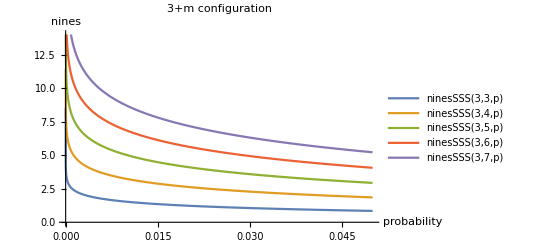

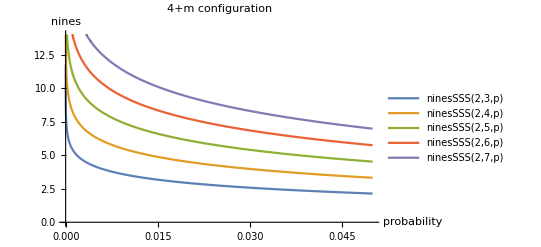

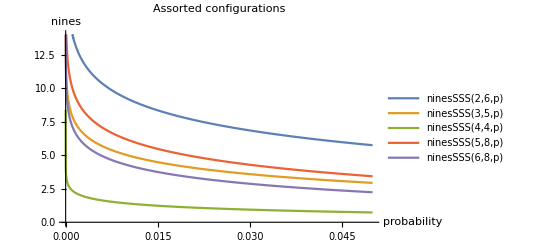

```mathematica
pSurvivalSSS[k_, n_, p_] = Sum[PDF[BinomialDistribution[n,p],i], {i, 0, n-k}]
pSurvivalRS[e_, d_, m_, p_] = Sum[PDF[BinomialDistribution[e+m,p], i], {i, 0, m-d}]
pSurvivalAONT[d_, m_, p_] = Sum[PDF[BinomialDistribution[m+d, p], i], {i, 0, m}]
ninesSSS[k_, n_, p_] = -Log[10, 1-pSurvivalSSS[k,n,p]]
ninesRS[e_, d_, m_, p_] = -Log[10, 1-pSurvivalRS[e, d,m,p]]
ninesAONT[d_, m_, p_] = -Log[10, 1-pSurvivalAONT[d,m,p]]
Plot[{ninesSSS[3,3,p],ninesSSS[3,4,p],ninesSSS[3,5,p],ninesSSS[3,6,p],ninesSSS[3,7,p]}, {p, 0, 0.05}, PlotRange -> {{0,0.05},{0,14}}, PlotLegends->LineLegend["Expressions"],PlotLabel->"3+m configuration", AxesLabel->{"probability", "nines"}]
Plot[{ninesSSS[2,3,p],ninesSSS[2,4,p],ninesSSS[2,5,p],ninesSSS[2,6,p],ninesSSS[2,7,p]}, {p, 0, 0.05}, PlotRange -> {{0,0.05},{0,14}}, PlotLegends->LineLegend["Expressions"],PlotLabel->"4+m configuration", AxesLabel->{"probability", "nines"}]
Plot[{ninesSSS[2,6,p],ninesSSS[3,5,p],ninesSSS[4,4,p],ninesSSS[5,8,p],ninesSSS[6,8,p]}, {p, 0, 0.05}, PlotRange -> {{0,0.05},{0,14}}, PlotLegends->LineLegend["Expressions"],PlotLabel->"Assorted configurations", AxesLabel->{"probability", "nines"}]
```

```mathematica
Piecewise[{{(1-p)^(e+m), (d-m==0&&d+e>0)||(d+e≤0&&e+m==0)}, {((1-p)^e p^-d (-(1/(1-p))^(e+m) (1-p)^m p^d+(1/(1-p))^(e+m) (1-p)^m p^(1+d)+(1-p)^d p^(1+m) Binomial[e+m,1-d+m] Hypergeometric2F1[1,1-d-e,2-d+m,p/(-1+p)]))/(-1+p), d+e>0&&d-m<0}, {((1-p)^(e+m-Floor[e+m]) (-(1/(1-p))^(e+m) (1-p)^Floor[e+m]+(1/(1-p))^(e+m) (1-p)^Floor[e+m] p+p^(1+Floor[e+m]) Binomial[e+m,1+Floor[e+m]] Hypergeometric2F1[1,1-e-m+Floor[e+m],2+Floor[e+m],p/(-1+p)]))/(-1+p), d+e≤0&&e+m>0}, {0, True}}]
```

Piecewise[{{(1-p)^(e+m), (d-m==0&&d+e>0)||(d+e≤0&&e+m==0)}, {((1-p)^e p^-d (-(1/(1-p))^(e+m) (1-p)^m p^d+(1/(1-p))^(e+m) (1-p)^m p^(1+d)+(1-p)^d p^(1+m) Binomial[e+m,1-d+m] Hypergeometric2F1[1,1-d-e,2-d+m,p/(-1+p)]))/(-1+p), d+e>0&&d-m<0}, {((1-p)^(e+m-Floor[e+m]) (-(1/(1-p))^(e+m) (1-p)^Floor[e+m]+(1/(1-p))^(e+m) (1-p)^Floor[e+m] p+p^(1+Floor[e+m]) Binomial[e+m,1+Floor[e+m]] Hypergeometric2F1[1,1-e-m+Floor[e+m],2+Floor[e+m],p/(-1+p)]))/(-1+p), d+e≤0&&e+m>0}, {0, True}}]

This highlights that when the probability of block overwrite is small then the probability of k out of n=m+k blocks surviving is rather promising.
The following equations show The probability that a Artifice instance of sizeM survives a given time between repair cycles.

```mathematica
pSurArtSSS[sizeM_, k_, m_, p_] = (pSurvivalSSS[k, m, p])^sizeM
pSurArtRS[sizeM, e_, d_, m_, p_] = (pSurvivalRS[e, d, m, p])^sizeM
pSurArtAONT[sizeM, d_, m_, p_] = (pSurvivalAONT[d, m, p])^sizeM
ninesMSSS[sizeM_, k_, m_, p_] = -Log[10, 1- pSurArtSSS[sizeM, k, m, p]]
```

(Piecewise[{{1, k≤0&&m>0}, {(1-p)^m, (m==0&&k≤0)||(k>0&&k-m==0)}, {(p^-k (-(1/(1-p))^m (1-p)^m p^k+(1/(1-p))^m (1-p)^m p^(1+k)+(1-p)^k p^(1+m) Binomial[m,1-k+m] Hypergeometric2F1[1,1-k,2-k+m,p/(-1+p)]))/(-1+p), k>0&&k-m<0}, {0, True}}])^sizeM

(Piecewise[{{(1-p)^(e+m), (d-m==0&&d+e>0)||(d+e≤0&&e+m==0)}, {((1-p)^e p^-d (-(1/(1-p))^(e+m) (1-p)^m p^d+(1/(1-p))^(e+m) (1-p)^m p^(1+d)+(1-p)^d p^(1+m) Binomial[e+m,1-d+m] Hypergeometric2F1[1,1-d-e,2-d+m,p/(-1+p)]))/(-1+p), d+e>0&&d-m<0}, {((1-p)^(e+m-Floor[e+m]) (-(1/(1-p))^(e+m) (1-p)^Floor[e+m]+(1/(1-p))^(e+m) (1-p)^Floor[e+m] p+p^(1+Floor[e+m]) Binomial[e+m,1+Floor[e+m]] Hypergeometric2F1[1,1-e-m+Floor[e+m],2+Floor[e+m],p/(-1+p)]))/(-1+p), d+e≤0&&e+m>0}, {0, True}}])^sizeM

(Piecewise[{{(1-p)^(d+m), (m==0&&d>0)||(d≤0&&d+m==0)}, {((1-p)^d (-(1/(1-p))^d+(1/(1-p))^d p+p^(1+m) Binomial[d+m,1+m] Hypergeometric2F1[1,1-d,2+m,p/(-1+p)]))/(-1+p), d>0&&m>0}, {((1-p)^(d-Floor[d]) (-(1/(1-p))^d (1-p)^Floor[d]+(1/(1-p))^d (1-p)^Floor[d] p+p^(1+m+Floor[d]) Binomial[d+m,1+m+Floor[d]] Hypergeometric2F1[1,1-d+Floor[d],2+m+Floor[d],p/(-1+p)]))/(-1+p), d≤0&&d+m>0}, {0, True}}])^sizeM

-Log[1-(Piecewise[{{1, k≤0&&m>0}, {(1-p)^m, (m==0&&k≤0)||(k>0&&k-m==0)}, {(p^-k (-(1/(1-p))^m (1-p)^m p^k+(1/(1-p))^m (1-p)^m p^(1+k)+(1-p)^k p^(1+m) Binomial[m,1-k+m] Hypergeometric2F1[1,1-k,2-k+m,p/(-1+p)]))/(-1+p), k>0&&k-m<0}, {0, True}}])^sizeM]/Log[10]

If we assume that Artifice is allowed to repair each night and that the host file system is used to write 5GB of data a day.  We can then determine the probability of a block being selected and written to. This is very much the same as Thomas’ calculations. The distribution of overwritten blocks is uniform, other distributions should be applied to better model different file systems. We can possibly gather data on different systems from lab machines to build these distributions. Other than that the best way to make this more sophisticated is to skip the theoretical work and go right to experiments.

```mathematica
nrBlocksCleared = 5*2^30 / blocksize
```

1310720

```mathematica
ps = (nrBlocksCleared / nrBlocks)// N
```

0.00976563

At minimum our file system will need to have its metadata survive. This includes a superblock and a table to contain mappings and checksums of our hidden blocks. For a 5GB system with 4 parity blocks, two entropy blocks, and two data blocks we will need approximately 300MB (6.45%) for the metadata (yes that is quite big). We keep track of much more information about Artifice in order to manage mapping logical Artifice blocks to tuples of physical blocks via our device mapper. Therefore our metadata costs increase considerably compared to a normal file system. The map consists of three layers. A set of blocks that contain pointers to other blocks in the map. The second layer is a set of blocks that keep track of erasure coding information for the map block itself. The third layer is the actual map blocks that contain information about the carrier blocks.

```mathematica
matSize = (5*2^30)/(4*2^10)
```

1310720

```mathematica
carrierblocktuple = 4+2
```

6

```mathematica
matblockhash= 16
```

16

```mathematica
EntropyNameHash = 8
```

8

```mathematica
8
PointerSize =4
Replicas = 8
```

8

4

8

Represents the write amplification factor.  So if we have four parity blocks and two data blocks corresponding to an entry we end up having to write two carrier blocks for each data block. Therefore an amplification factor of two. This does not consider entropy blocks as those would be in a separate location.

```mathematica
amplificationFactorRS[parityBlocksPerEntry_, dataBlocksPerEntry_] := parityBlocksPerEntry/ dataBlocksPerEntry
amplificationFactorAONT[parityBlocksPerEntry_, dataBlocksPerEntry_] := (parityBlocksPerEntry + dataBlocksPerEntry)/ dataBlocksPerEntry
```

Total size of a record in the artifice map.

```mathematica
recordsizeRS[entropy_, parity_, data_] := ((entropy+parity)*carrierblocktuple) + matblockhash + EntropyNameHash
recordsizeSSS[numshares_] := (numshares * carrierblocktuple) + matblockhash
recordsizeAONT[parity_, data_] := ((parity+data) * carrierblocktuple) + matblockhash
```

Entries stored in each 4KB map block. There is a 64 byte hash stored at the start of the map block. Have to make sure to round down to the nearest whole number.

```mathematica
entriesperblockRS[entropy_, parity_, data_] := Floor[((4*2^10 - 64)/ recordsizeRS[entropy, parity,data])]
entriesperblockSSS[shares_] := Floor[((4*2^10 - 64)/ recordsizeSSS[shares])]
entriesperblockAONT[parity_, data_] := Floor[((4*2^10 - 64)/ recordsizeAONT[parity,data])]
```

Calculates the overall number of map blocks needed.

```mathematica
nummapblocksRS[blocks_, entropy_, parity_, data_] := Ceiling[blocks / entriesperblockRS[entropy,parity,data]]
nummapblocksSSS[blocks_, shares_] := Ceiling[blocks / entriesperblockSSS[shares]]
nummapblocksAONT[blocks_, parity_, data_] := Ceiling[blocks / entriesperblockAONT[parity,data]]
```

The number of blocks needed to serve as map blocks for the map blocks. This is so we can protect a good chunk of the metadata with our IDA. We also calculate the number of pointer blocks, this additionally takes in the number of replicas, as we are replicating the pointer blocks and super block, which are each encrypted with a unique IV (derived from the passphrase with a cryptographic hash).

```mathematica
nummapmapblocksRS[blocks_, entropy_, parity_, data_] := Ceiling[nummapblocksRS[blocks, entropy, parity, data] / entriesperblockRS[entropy,parity,data]]
nummapmapblocksSSS[blocks_, shares_] := Ceiling[nummapblocksSSS[blocks, shares] / entriesperblockSSS[shares]]
nummapmapblocksAONT[blocks_, parity_, data_] := Ceiling[nummapblocksAONT[blocks,parity, data]/ entriesperblockAONT[parity,data]]

numpointerblocksRS[blocks_, entropy_, parity_, data_] := Ceiling[nummapmapblocksRS[blocks, entropy, parity, data]/((blocksize/PointerSize) -1)]
numpointerblocksSSS[blocks_,shares_] := Ceiling[nummapmapblocksSSS[blocks, shares]/((blocksize/PointerSize) -1)]
numpointerblocksSSSReplicas[blocks_,shares_] := Ceiling[nummapblocksSSS[blocks, shares]/((blocksize/PointerSize) -1)]
numpointerblocksAONT[blocks_, parity_, data_] := Ceiling[nummapmapblocksAONT[blocks, parity, data]/((blocksize/PointerSize) -1)]
```

Calculate the overall metadata size in 4KB blocks given parameters for a map block entry and the total size of the artifice instance. Any left over space in a block should be filled with data from the same randomness source as the rest of Artifice.

```mathematica
calcMetadataSizeRS[blocks_, parity_, entropy_, data_] := Replicas *(numpointerblocksRS[blocks, entropy, parity, data]+nummapmapblocksRS[blocks, entropy, parity, data]) + (nummapblocksRS[blocks, entropy, parity, data] * amplificationFactorRS[parity,data])
calcMetadataSizeSSS[blocks_, shares_] := Replicas * (numpointerblocksSSS[blocks,shares]+nummapmapblocksSSS[blocks, shares]) + (nummapblocksSSS[blocks, shares] * shares)
calcMetadataSizeSSSReplication[blocks_, shares_] :=(numpointerblocksSSSReplicas[blocks,shares]+ nummapblocksSSS[blocks, shares]) * Replicas
calcMetadataSizeAONT[blocks_, parity_, data_] := Replicas*(numpointerblocksAONT[blocks, parity, data]+nummapmapblocksAONT[blocks, parity, data]) + (nummapblocksAONT[blocks, parity, data] * amplificationFactorAONT[parity,data])
```

```mathematica
metadataSize = calcMetadataSizeSSS[matSize,6]
```

103922

```mathematica
metadatasizeReplcias = calcMetadataSizeSSSReplication[matSize, 6]
```

136320

We want to be able to survive for about five year’s worth of invocations with writing 5 GB per day. Allowing for repair each day.

```mathematica
nrDays = Round[365.25 * 1]
```

365

For calculating metadata size we assume that the number of data blocks is always 2.

General::munfl: 0.999065^(2.8007×10^7) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.952133^(2.8007×10^7) is too small to represent as a normalized machine number; precision may be lost.

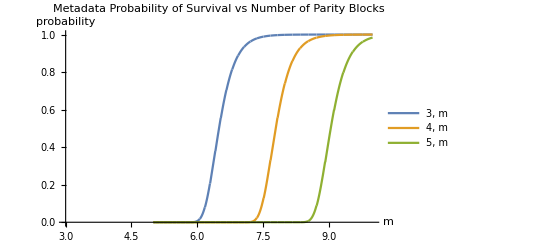

```mathematica
probArtAliveRS[entropy_, data_,  parity_] := (pSurvivalRS[entropy, data, parity,  ps])^(calcMetadataSizeRS[matSize, parity, entropy, data] * nrDays)
probArtAliveSSS[threshold_, shares_] := (pSurvivalSSS[threshold, shares, ps])^(calcMetadataSizeSSS[matSize, shares] * nrDays)
probArtAliveAONT[data_, parity_] := (pSurvivalAONT[data, parity, ps])^(calcMetadataSizeAONT[matSize, parity, data] * nrDays)
metasurviveSSS = Plot[{probArtAliveSSS[3, m],probArtAliveSSS[4,m],probArtAliveSSS[5,m]}, {m, 5, 10}, PlotRange->{{3, 10}, {0,1}}, PlotLabel->"Metadata Probability of Survival vs Number of Parity Blocks",PlotLegends -> Placed[LineLegend[{"3, m", "4, m", "5, m"},LegendMarkerSize->{25, 15}], {{0.9,0.3}}], AxesLabel->{"m", "probability"}]
```

```mathematica
Export["metasurviveSSS.png", metasurviveSSS, ImageResolution -> 200]
```

metasurviveSSS.png

A bit of numerical issues around 7 or more nines aside. This shows us that the even though we have increased the metadata size considerably our system still returns about six nines with a 3+7 configuration. So about a 99.9999% chance of survival. When compared with Thomas Schwarz’s results we can see that the numerical issues appear even when dealing with just the metadata.

This following function outputs the total size of the artifice instance on disk accounting for write amplification (we assume that the 5GB is utilizable memory).

```mathematica
SizeTotal[size_, parity_, data_] := size * (parity/data)
```

(Piecewise[{{1, k≤0&&m>0}, {0.990234^m, (m==0&&k≤0)||(k>0&&k-m==0)}, {-1.00986 0.00976563^-k (-1. 0.00976563^k+1. 0.00976563^(1+k)+0.00976563^(1+m) 0.990234^k Binomial[m,1-k+m] Hypergeometric2F1[1,1-k,2-k+m,-0.00986193]), k>0&&k-m<0}, {0, True}}])^((478412800 m)/k)

/home/austen/programming/dm-afs

General::munfl: 0.999991^(7.97377×10^8) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.999065^(5.98033×10^8) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 0.952139^(4.78426×10^8) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

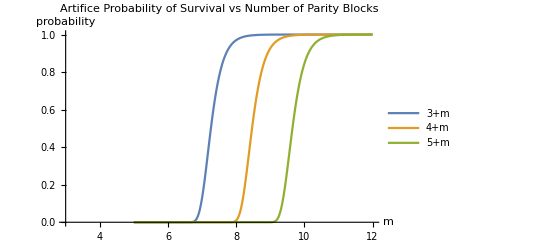

matsurvive.png

```mathematica
probArtAllAliveSSS[k_,m_] = pSurvivalSSS[k, m, ps]^(SizeTotal[matSize, m, k] * nrDays)
SetDirectory[NotebookDirectory[]]
matsurviveSSS =Plot[{probArtAllAliveSSS[3, m],probArtAllAliveSSS[4, m],probArtAllAliveSSS[5, m]}, {m, 5, 12}, PlotLabel->"Artifice Probability of Survival vs Number of Parity Blocks", PlotRange->{{3, 12}, {0,1}}, PlotLegends -> Placed[LineLegend[{"3+m", "4+m", "5+m"}, LegendMarkerSize->{25, 15}],{{0.9,0.3}}], AxesLabel->{"m", "probability"}]
Export["matsurvive.png", matsurviveSSS, ImageResolution -> 200]
```

```mathematica
"/home/austen/Desktop"
```

/home/austen/Desktop

```mathematica
ExpandFileName["/home/austen/Desktop"]
```

/home/austen/Desktop

```mathematica
SystemOpen["/home/austen/Desktop"]
```

We can see again that even with the numerical issues there is a rather good chance of survival with five nines when in a 3+7 configuration. So a 99.999% chance of survival. As with Thomas Schwarz’s previous calculations we can compare this favorably to a disk with a MTTF of 200,000 hours.

```mathematica
pDiskSurvives5Years = ((1-(1/200000))^(nrDays*24))//N
```

0.957145

As with Thomas’ calculations we don’t assume careful selection of free blocks in the file system. If we were to more closely tailor the system to the allocation behavior of each file system then the results would likely improve.